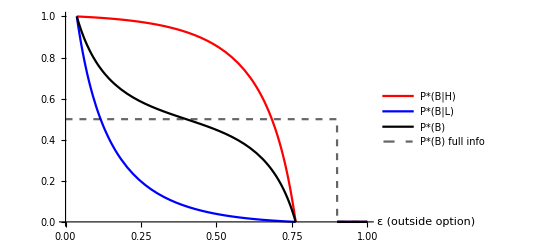

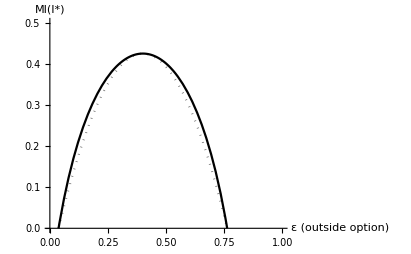

```mathematica
ClearAll[r,cond1,cond2,cond3,cond4,Pif,PiI,TotalPi,MI,optimize];

r[λ_]:=Exp[-1/λ];

cond1[x_,w_,λ_,p1_]:=0<x<λ*Log[2/(Exp[-1/λ]+1)]-w-p1;
cond2[x_, w_,λ_,p1_]:=λ*Log[2/(Exp[-1/λ]+1)]-w-p1<x<-λ Log[2/(Exp[1/λ]+1)]-w-p1;
cond3[x_,w_,λ_,p1_]:=1>x>-λ Log[2/(Exp[1/λ]+1)]-w-p1;
cond4[w_,λ_]:=λ<0.01;

MI[x_,w_,λ_,p1_]:=1/2*((Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])) Log[2]+(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)]+(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1])/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])]-(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))Log[(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))]+(B[x,w,λ,p1] Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)Log[(B[x,w,λ,p1] Exp[-1/λ]^2-2 Exp[-1/λ]+Exp[-1/λ] B[x,w,λ,p1])/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)]+(Exp[-1/λ] B[x,w,λ,p1]+B[x,w,λ,p1]-2)/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])Log[(Exp[-1/λ] B[x,w,λ,p1]+B[x,w,λ,p1]-2)/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])]-(2-(Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1])))Log[1-1/2 (Exp[-1/λ]+1-2 Exp[-1/λ] B[x,w,λ,p1]) (1/(B[x,w,λ,p1] Exp[-1/λ]^2-Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]+1)+1/(Exp[-1/λ]-Exp[-1/λ] B[x,w,λ,p1]-1+B[x,w,λ,p1]))]);

B[x_,w_,λ_,p1_]=Exp[(x+w+p1)/λ];
H[x_,w_,λ_,p1_]=(r[λ]+1-2r[λ]B[x,w,λ,p1])/(B[x,w,λ,p1]r[λ]^2-r[λ]-r[λ]B[x,w,λ,p1]+1);
L[x_,w_,λ_,p1_]=(r[λ]+1-2r[λ]B[x,w,λ,p1])/(r[λ]+B[x,w,λ,p1]-r[λ]B[x,w,λ,p1]-1);
U[x_,w_,λ_,p1_]:=Piecewise[{
{0.5-w-p1,cond1[x,w,λ,p1]},
{0.5(H[x,w,λ,p1]*(1-w-p1)+L[x,w,λ,p1]*(-w-p1)+(2-H[x,w,λ,p1]-L[x,w,λ,p1])*x)-λ*MI[x,w,λ,p1],cond2[x,w,λ,p1]},
{x,cond3[x,w,λ,p1]}
}];
FullInfo[x_,w_,p1_]:=Piecewise[{
{1,x<-p1-w},
{0.5,-p1-w<x<1-p1-w},
{0,x>1-p1-w}
}];

Plot[{Piecewise[{{H[x,0,0.2,0.1],x<0.9}}],Piecewise[{{L[x,0,0.2,0.1],x<0.9}}],Piecewise[{{(H[x,0,0.2,0.1]+L[x,0,0.2,0.1])/2,x<0.9}}],FullInfo[x,0,0.1]},{x,0,1}, PlotRange->{0,1},PlotStyle->{Red,Blue, Black,{Black,Dashed,Opacity[0.6]}},AxesLabel->{"ε (outside option)"},PlotLegends->{"P*(B|H)","P*(B|L)","P*(B)","P*(B) full info"}]
eps0[x_, w_, λ_, p1_] := λ*Log[2/(1 + Exp[-1/λ])] - w-p1;
eps1[x_, w_, λ_, p1_] := -λ*Log[2/(Exp[1/λ] + 1)] - w-p1;

x0[x_, w_, λ_,p1_] :=(eps0[x, w, λ, p1]+eps1[x, w, λ, p1])/2;
MIapprox[x_,w_,λ_,p1_]:=-4((H[x0[x,w,λ,p1], w, λ, p1]*Log[2H[x0[x,w,λ,p1], w, λ, p1]]+L[x0[x,w,λ,p1], w, λ, p1]*Log[2L[x0[x,w,λ,p1], w, λ, p1]])/(-eps0[x, w, λ, p1]+eps1[x, w, λ, p1])^2)*(x-eps0[x, w, λ, p1])*(x-eps1[x, w, λ, p1]);

Plot[{MI[x,0,0.2,0.1],MIapprox[x,0,0.2,0.1]},{x,0,1}, PlotRange->{0,0.5},PlotStyle->{Black,{Black,Dotted,Opacity[0.6]}},AxesLabel->{"ε (outside option)", "MI(I*)"}]
```

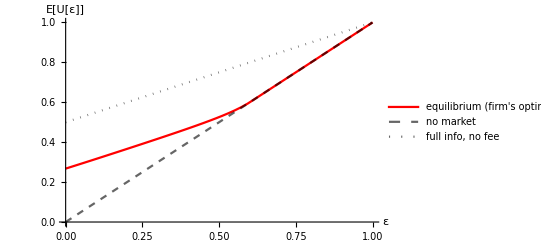

0.652858

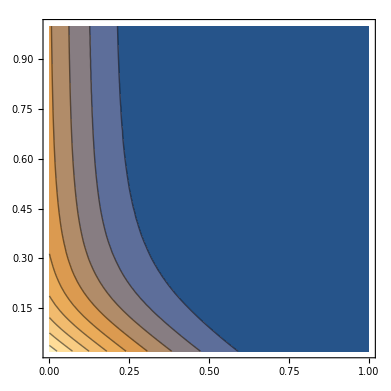

General::munfl: Exp[-99000.] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::munfl: Exp[-99000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.30386×10^13}. NIntegrate obtained 0.00128109 and 0.000106899 for the integral and error estimates.

-Graphics-

```mathematica
Plot[{U[x,0.13,0.1,0.2],x, Max[x,(1+x)/2]},{x,0,1}, PlotRange->{0,1},PlotStyle->{Red,{Black,Dashed,Opacity[0.6]}, {Black,Dotted,Opacity[0.6]}},AxesLabel->{"ε","E[U[ε]]"},PlotLegends->{"equilibrium (firm's optimum)","no market","full info, no fee"}]


Ueval[w_?NumericQ,λ_?NumericQ]/;λ>0.02:=NIntegrate[U[x,w,λ,0.1],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->10,AccuracyGoal->6,PrecisionGoal->6]

Ueval[0.05,0.05]
ContourPlot[Evaluate@Ueval[w,λ],{w,0,1},{λ,0.02,1},PlotPoints->15,MaxRecursion->2,Exclusions->None,PlotRange->All]
```

```mathematica
ClearAll[optimize];
cond1[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=TrueQ@N[2/(Exp[-1/λ]+1)>=Exp[(w+p1)/λ]];

cond2[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=Module[{z},z=N@Exp[(w+p1)/λ];
TrueQ@N[2/(Exp[-1/λ]+1)<z<=(Exp[-1/λ]+1)/(2 Exp[-1/λ])]];

cond3[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=TrueQ@N[Exp[(w+p1)/λ]>(Exp[-1/λ]+1)/(2 Exp[-1/λ])];

cond4[w_?NumericQ,λ_?NumericQ]:=λ<0.01;


Pif[w_?NumericQ,λ_?NumericQ,p1_?NumericQ]:=Module[{},Which[cond4[w,λ],w p1 (1-w-p1)/2,cond1[w,λ,p1],p1 w (1/2-w-p1),cond2[w,λ,p1],(p1 w λ/2)*(Log[((r[λ]+1)/(2 r[λ])-1)/(Exp[(w+p1)/λ]-1)]+Log[(r[λ] ((r[λ]+1)/(2 r[λ]))-1)/(r[λ] Exp[(w+p1)/λ]-1)]),True,0]]

PiI[w_?NumericQ,λ_?NumericQ,p1_?NumericQ,p2_?NumericQ]:=Module[{},Which[cond4[w,λ],0,cond1[w,λ,p1],NIntegrate[p2*MI[λ,x] λ^2/x,{x,2/(Exp[-1/λ]+1),(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],cond2[w,λ,p1],NIntegrate[p2*MI[λ,x] λ^2/x,{x,Exp[(w+p1)/λ],(Exp[-1/λ]+1)/(2 Exp[-1/λ])}],True,0]]

TotalPi[w_?NumericQ,λ_?NumericQ,p1_?NumericQ,p2_?NumericQ]:=Pif[w,λ,p1]+PiI[w,λ,p1,p2];

optimize[p1_?NumericQ,p2_?NumericQ]:=Module[{res},res=FindMaximum[TotalPi[w,λ,p1,p2],{{w,0.2,0,1},{λ,0.1,0,1}}];
<|"p1"->p1,"p2"->p2,"PiMax"->res[[1]],"wStar"->w/. res[[2]],"λStar"->λ/. res[[2]]|>]
p1grid=Range[0.05,0.8,0.01];
p2grid=Range[0.05,8,0.1];

data=Flatten[Table[optimize[p1,p2],{p1,p1grid},{p2,p2grid}],1];
piData=data[[All,{"p1","p2","PiMax"}]]//Values;
wData=data[[All,{"p1","p2","wStar"}]]//Values;
λData=data[[All,{"p1","p2","λStar"}]]//Values;

contourStyle={InterpolationOrder->2,ColorFunction->"ThermometerColors",PlotRange->All,Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[14],PlotLegends->BarLegend[Automatic]};


n1=Length[p1grid];
n2=Length[p2grid];

piVals=ArrayReshape[piData[[All,3]],{n1,n2}];

piIF=ListInterpolation[piVals,{p1grid,p2grid},InterpolationOrder->3];

wVals=ArrayReshape[piData[[All,3]],{n1,n2}];

wIF=ListInterpolation[wVals,{p1grid,p2grid},InterpolationOrder->3];

λVals=ArrayReshape[λData[[All,3]],{n1,n2}];

λIF=ListInterpolation[λVals,{p1grid,p2grid},InterpolationOrder->3];



plot1=ContourPlot[piIF[p1,p2],{p1,Min@p1grid,Max@p1grid},{p2,Min@p2grid,Max@p2grid},Contours->30,PlotLegends->BarLegend[Automatic],ColorFunction->"ThermometerColors",FrameLabel->{"p1","p2","π^*"},PlotLabel->Style["Equilibrium Profit (π^*)",16,Bold],Frame->True]
plot2=ContourPlot[wIF[p1,p2],{p1,Min@p1grid,Max@p1grid},{p2,Min@p2grid,Max@p2grid},Contours->30,PlotLegends->BarLegend[Automatic],ColorFunction->"ThermometerColors",FrameLabel->{"p1","p2","w^*"},PlotLabel->Style["Equilibrium Fee(w^*)",16,Bold],Frame->True]
plot3=ContourPlot[λIF[p1,p2],{p1,Min@p1grid,Max@p1grid},{p2,Min@p2grid,Max@p2grid},Contours->30,PlotLegends->BarLegend[Automatic],ColorFunction->"ThermometerColors",FrameLabel->{"p1","p2","λ^*"},PlotLabel->Style["Equilibrium Attention Cost(λ^*)",16,Bold],Frame->True]
```